## 3 Asymptotic analysis of the swallowtail catastrophe

This intent of this notebook is to model the analysis done in section 3 of the paper Automorphisms of Stokes multipliers in higher-order WKBJ theory by Shelton et al.

```mathematica
(* Invoked to check derived expressions with paper's analysis *)
check[label_,cond_]:=Framed[Row[{Which[cond===True,"✅ ",cond===False,"❌ ",True,"⚠️ "],label,": ",cond}],Background->Which[cond===True,Lighter[Green,0.7],cond===False,Lighter[Red,0.7],True,Lighter[Yellow,0.7]],FrameStyle->None,FrameMargins->5,RoundingRadius->4]
```

## Section 3.1

The swallowtail integral is a fundamental integral of catastrophe theory, with a quintic phase in the integration variable and three real parameters.

```mathematica
phaseIntegrandPsi[t_]:=I(t^5 + x3 t^3 + x2 t^2 + x1 t);
integrandPsi[t_] :=Exp[phaseIntegrandPsi[t]];

(* Equation(3.1)*)
Psi[x1_, x2_, x3_]:=
Integrate[
integrandPsi[t]
,{t, -Infinity, Infinity}
]
```

The integral satisfies a fourth-order linear ODE in 𝑥_1 with x_2 and x_3 entering as parameters.
	​
The unknown is written 𝑌 to keep it distinct from the integral above.

```mathematica
swallowtailODE = 5 Y''''[x1] - 3x3 Y''[x1] - 2 I x2 Y'[x1] + x1 Y[x1];

(* Equation (3.2)*)
swallowtailODEObject = swallowtailODE ==0
```

x1 Y[x1]-2 ⅈ x2 Y'[x1]-3 x3 Y''[x1]+5 Y^(4)[x1]==0

A far-field rescaling introduces the small parameter 𝜖, so that the large x_1 asymptotics of Ψ become the small  𝜖 asymptotics of 𝜓. 

The integration variable is rotated by 𝑡 ↦−𝑖𝑡, which brings the exponent to the standard steepest-descent form.

Note that the t rotation includes a eps^(-1/5) factor which is not mentioned in the paper.

```mathematica
rescaleRules = {
x1 ->z eps^(-4/5),
x2 -> b eps^(-3/5),
x3 -> a eps^(-2/5)
};
tRotateRule = {
t-> -I t eps^(-1/5)
};

fDerived=(phaseIntegrandPsi[t]/. rescaleRules/. tRotateRule) eps;
f[t_,z_]:= t^5 - a t^3 - I b t^2 + z t;
check["fDerived equals paper's f[t,z]",Simplify[fDerived - f[t,z]]== 0 ]
```

✅ fDerived equals paper's f[t,z]: True

```mathematica
integrandLowercasePsi[t_,z_]:=Exp[f[t,z]/eps]

(* Equation (3.4)*)
lowercasePsi[z_]:=(1/(I eps^(1/5)))*Integrate[integrandLowercasePsi[t,z],{t,L}];
```

Substituting the rescalings into (3.2) gives the rescaled ODE. The chain rule contributes a factor 𝜖^(4k/5) to each derivative of order 𝑘.

```mathematica
derivRules={
Y''''[x1]->eps^(16/5) psi''''[z],
Y''[x1]->eps^(8/5) psi''[z],
Y'[x1]->eps^(4/5) psi'[z],
Y[x1]->psi[z] 
};

rescaledSwallowtailODE=swallowtailODE /. derivRules /.rescaleRules // Simplify;

(* Equation (3.5a),normalised so the z psi term carries no eps *)
rescaledSwallowtailODEObject= eps^(4/5) rescaledSwallowtailODE==0;
```

The far-field condition selects the integral solution: as ∣z∣ → ∞  along arg z = −3π/4, only one of the four WKBJ components is present.

```mathematica
alpha = Exp[3 I Pi/4];

(*Equation (3.5b)*)
psiFarField[z_]:=
(-I Sqrt[Pi]) / (Sqrt[2 * 5^(1/4) * alpha^3 * z^(3/4)]) * Exp[ -(4 alpha z^(5/4) / (5^(5/4) eps))];
```

## Section 3.2 — The asymptotic transseries

The transseries consists of four WKBJ components, each an amplitude multiplying an exponential of a singulant. Since the ODE is linear and the exponentials are independent, the equations for the singulant and amplitude follow from substituting a single generic component.

```mathematica
(*Equation (3.6)*)
wkbjComponent[i_]:=amp[i][z] Exp[-chi[i][z]/eps];
transseries=Sum[wkbjComponent[i],{i,1,4}];

singleComponent[z_]:=amp[z] Exp[-chi[z]/eps];

psiToSingleComponentRule = psi -> Function[zz, singleComponent[zz]];
odePsiToSingleComponentRule = rescaledSwallowtailODE /. psiToSingleComponentRule;

rescaledSwallowtailODESingleComponent=Simplify[
odePsiToSingleComponentRule/Exp[-chi[z]/eps] * eps^(4/5)
];
```

Balancing powers of ϵ gives the singulant equation at leading order, a quartic for χ'.

```mathematica
leadingOrder=Coefficient[
rescaledSwallowtailODESingleComponent 
,eps,0];

singulantEqnDerived = Simplify[leadingOrder/ amp[z]] == 0;
(* Corrected Equation (3.7), NB: Prefactor of 5 is missing in front of quartic term in (3.7) *)
singulantEqn = 5chi'[z]^4 - 3a chi'[z]^2 + 2 I b chi'[z] + z ==0;

check["singulantEqnDerived equals (corrected)paper's equation (3.7)", singulantEqnDerived == singulantEqn]
```

✅ singulantEqnDerived equals (corrected)paper's equation (3.7): True

The remaining orders give the amplitude equation. Expanding the amplitude in powers of ϵ and taking the leading balance yields the transport equation, whose solution is the leading-order amplitude.

```mathematica
(*Equation (3.8)*)
nextToLeadingOrder = Simplify[
(rescaledSwallowtailODESingleComponent - leadingOrder)/eps 
];

(*Equation (3.9)*)
nmax=2;
ampExpansionRule=amp->Function[zz,Sum[eps^n ampn[n][zz],{n,0,nmax}]];

transportEqnDerived=Coefficient[
nextToLeadingOrder /. ampExpansionRule
,eps,0]==0 ;
(*Equation (3.10); ampn[0][z] = Subscript[ψ, 0]^n(z)*)
transportEqn =(-20chi'[z]^3 + 6a chi'[z]-2 I b)ampn[0]'[z] +(3 a chi''[z]- 30 chi''[z]chi'[z]^2)ampn[0][z] ==0;

check["transportEqnDerived equals paper's (3.10)", transportEqnDerived==transportEqn//Expand]
```

✅ transportEqnDerived equals paper's (3.10): True

```mathematica
(*Equation (3.11);the integration constant is fixed to Sqrt[Pi]; NB: There is a sign difference compared to (3.11)*)
psi0=DSolve[transportEqn,ampn[0][z],z];
```

### Section 3.2.1 — Singular points

The leading amplitude is singular where its denominator vanishes. Solving that cubic for χ' and mapping through the singulant equation locates the three singular points in the 
z-plane; reduction modulo the cubic gives the compact form (3.12).

```mathematica
singularCubic=-10 t^3+3 a t-I b==0;
tRoots=t/. Solve[singularCubic,t];

zExpr=z/. First[Solve[singulantEqn/. chi'[z]->tt,z]];
zFromSingulant[t_]:=zExpr/. tt->t


zOfT = PolynomialReduce[zFromSingulant[t],First[singularCubic],t][[2]]//Simplify;
zOfTFunctionDerived[t_] := Evaluate[zOfT]
(*Equation (3.12)*)
zOfTFunction[t_] := (3t)/2(a t - I b)

check["zOfTFunctionDerived equals (3.12)", zOfTFunctionDerived[t] == zOfTFunction[t] //Simplify]
```

✅ zOfTFunctionDerived equals (3.12): True

For particular values of 𝑎 and 𝑏 the singular points coalesce. When 𝑎 = 𝑏 = 0 all three lie at the origin; when 𝑏 = 0 two coincide at 𝑧 = 9 𝑎^2/20.

```mathematica
(*Case a = b = 0*)
Block[{a=0,b=0},
Module[{derived, expected},
derived = zOfTFunction/@(t/. Solve[singularCubic,t]);
expected = {0, 0,0};
check["Derived z values for a = b = 0 equals paper's", derived == expected]
]
]

(*Case b = 0*)
Block[{b=0},
Module[{derived, expected},
derived = zOfTFunction/@(t/.Solve[singularCubic,t]);
expected = { (9 a^2)/20,(9 a^2)/20,0};
check["Derived z values for b = 0 equals paper's", Sort[Simplify[derived]] == Sort[Simplify[expected]]]
]
]
```

✅ Derived z values for a = b = 0 equals paper's: True

✅ Derived z values for b = 0 equals paper's: True

Two roots of the cubic coincide when its discriminant vanishes, giving the curved branches of Figure 1. The line 𝑏 = 0 is a separate locus, on which two distinct roots map to the same 𝑧.

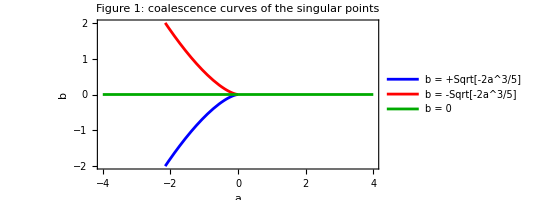

```mathematica
singularCubicDiscriminant=Discriminant[First[singularCubic],t];
coalescenceCurves=Solve[singularCubicDiscriminant==0,b]//Simplify;
branchExprs=b/. coalescenceCurves;

(*Figure 1*)
figure1=Plot[
Evaluate[Append[branchExprs,0]],(*the two branches plus b=0*)
{a,-4,4},
PlotStyle->{Blue,Red,Darker[Green]},
PlotRange->{{-4,4},{-2,2}},
AspectRatio->1/2,
Frame->True,
Axes->False,
FrameLabel->{"a","b"},
PlotLabel->"Figure 1: coalescence curves of the singular points",PlotLegends->Placed[{"b = +Sqrt[-2a^3/5]","b = -Sqrt[-2a^3/5]","b = 0"},Right],
Exclusions->None
]
```

## Section 3.3 — The singulant functions

The singulant follows from the saddle-point exponent. The saddles satisfy ∂_t 𝑓 = 0, and since ∂_z 𝑓 = 𝑡 the chain rule gives 𝑡_i = −𝜒_i'. Reduction of −𝑓(−𝜒', 𝑧) modulo the singulant equation yields the closed form.

```mathematica
(*Equation (3.16a),integral route*)
chiRouteA = PolynomialReduce[-f[-chi'[z],z],First[singulantEqn],chi'[z]][[2]];
```

The same result follows from the Hamilton–Jacobi system associated with the Borel operator. The symbol contains no 𝑤, so 
𝜂 is conserved and, with 𝜂(0) = 1, equals unity; 𝜉 is then linear in 𝜏. Integrating the remaining two equations gives 𝑧(𝜏) and 𝑤(𝜏), and 𝑧(𝜏) is recognised as the singulant quartic, identifying 𝜏 = 𝜒' and 𝑤 = 𝜒.

```mathematica
(*Equation (3.13)*)
borelSymbol=5 xi^4-3 a eta^2 xi^2-2 I b eta^3 xi+z eta^4;

(*Equation (3.14a)*)
zPrime=D[borelSymbol,xi];
wPrime=D[borelSymbol,eta];
xiPrime=-D[borelSymbol,z];
etaPrime=-D[borelSymbol,w];

etaAndXiRule={eta->1,xi->-tau};
zPrimeReduced=zPrime/. etaAndXiRule; 
wPrimeReduced=wPrime/. etaAndXiRule;

(*Equation (3.15a)*)
solZ=DSolve[{Z'[tau]==zPrimeReduced,Z[0]==0},Z[tau],tau]//First;
zOfTau=Z[tau]/. solZ//Expand;

(*Equation (3.15b);w' depends on z,which evolves along the characteristic*)
wPrimeReducedInTau=wPrimeReduced/. z->zOfTau//Expand;
solW=DSolve[{W'[tau]==wPrimeReducedInTau,W[0]==w0},W[tau],tau]//First;
wOfTau=W[tau]/. solW//Expand;

tauConstraint=Expand[z-zOfTau];

(*Equation (3.16a),Hamilton-Jacobi route*)
chiRouteB=PolynomialReduce[wOfTau,tauConstraint,tau][[2]]//Expand;
chiFunction[z]:=-(2a)/5 chi'[z]^3 + (3I b)/5 chi'[z]^2+(4z)/5 chi'[z]+w0

check["Routes A (integral) and B (Hamilton-Jacobi) give the same χ_i[z]",(chiRouteB/. {tau->chi'[z],w0->0})==chiRouteA]
check["Derived χ_i[z] equals (3.16a)", (chiRouteB /. tau->chi'[z])== chiFunction[z]]
```

✅ Routes A (integral) and B (Hamilton-Jacobi) give the same χ_i[z]: True

✅ Derived χ_i[z] equals (3.16a): True

## Section 3.4 — Determination of the Stokes constants

The Stokes constants are obtained from the steepest-descent geometry of the integral at a fixed point of the 𝑧-plane. The paths of steepest descent emerge from each saddle along the directions in which Re fdecreases.

```mathematica
zFixed=3+0.5 I;
(* NB: paper mentions (a,b) = (1,3) but used (a,b)=(3,1) in actual analysis*)
aVal=3;
bVal=1;

fT[t_]:=t^5-aVal t^3-I bVal t^2+zFixed t;
fTp[t_]:=Evaluate[D[fT[u],u]/. u->t];
fTpp[t_]:=Evaluate[D[fT[u],{u,2}]/. u->t];

check["fT[t] is equal to f[t,zFixed]",Simplify[fT[t]-(f[t,zFixed]/. {a->aVal,b->bVal})]==0]

saddles=t/. NSolve[fTp[t]==0,t];
fSaddle[k_]:=fT[saddles[[k]]];
chiOf[k_]:=-fSaddle[k];

Module[{derived,expected},
derived=chiOf/@Range[Length[saddles]];
expected={-1.0464+0.7948 I,-1.1944+0.0920 I,1.2212+2.0196 I,1.0196+0.6936 I};
check["Singulants chi_i at z = 3 + 0.5 I and (a,b)=(3,1) equal paper's (3.19)",Sort[Round[derived,10^-4]]==Sort[Round[expected,10^-4]]]
]
```

✅ fT[t] is equal to f[t,zFixed]: True

✅ Singulants chi_i at z = 3 + 0.5 I and (a,b)=(3,1) equal paper's (3.19): True

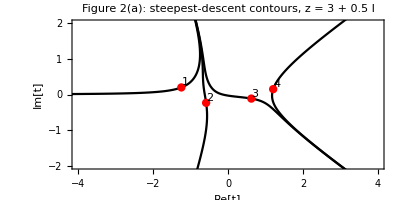

```mathematica
(*Local expansion f(t)- f(t_i)∼(1/2) f''(t_i) delta^2. Writing f''(t_i)=R e^{I phi} and delta=r e^{I theta},descent requires f''(t_i) delta^2 real and negative,i.e.2 theta+phi=pi.The two solutions are the two descent arms of the saddle.*)
descentDirections[ti_]:=Module[{phi=Arg[fTpp[ti]]},{Exp[I (Pi-phi)/2],Exp[I ((Pi-phi)/2+Pi)]}
];

(*Steepest-descent path as the gradient flow of Re[f],dt/ds=-conj(f'(t)).The flow is normalised to unit speed so it does not stall where f' is small;
this changes the parametrisation but not the curve.
Integration starts a short step off the saddle along a descent direction,and stops on reaching a neighbouring saddle,where f' vanishes.*)
descentRay[ti_,dir_,sMax_:8]:=Module[{eps=10^-2},NDSolve[{t'[s]==-Conjugate[fTp[t[s]]]/(Abs[fTp[t[s]]]+10^-6),t[0]==ti+eps dir,WhenEvent[Abs[fTp[t[s]]]<10^-3,"StopIntegration"]},t,{s,0,sMax},MaxSteps->10^5][[1]]
];

(*Sample a solution over its own integration range and return it as a curve*)
rayLine[sol_]:=Module[{tf,sMin,sMax},
tf=t/. sol;
{sMin,sMax}=tf["Domain"][[1]];
Line[ReIm/@Table[tf[s],{s,sMin,sMax,(sMax-sMin)/400}]]
];

(*Two descent arms from each of the four saddles*)
allRays=Flatten[Table[With[{ti=saddles[[k]]},descentRay[ti,#]&/@descentDirections[ti]],{k,Length[saddles]}],1];

(*Figure 2(a):arg[eps]=0*)
figure2a=Graphics[{Black,Thickness[0.004],rayLine/@allRays,Red,PointSize[0.015],Point[ReIm/@saddles],Black,MapThread[Text[#2,ReIm[#1],{-1.5,-1.5}]&,{saddles,Range[4]}]},Frame->True,FrameLabel->{"Re[t]","Im[t]"},PlotRange->{{-4,4},{-2,2}},AspectRatio->1/2,PlotLabel->"Figure 2(a): steepest-descent contours, z = 3 + 0.5 I"]
```

the special steepest-descent curves C_j(σ_ij) are obtained by continuing arg ϵ from 0 to σ_ij= arg[χ_j- χ_i]. Panel i shows these three curves  together with the positively oriented contour about saddle i, which is deformed onto them to give the Stokes constants.

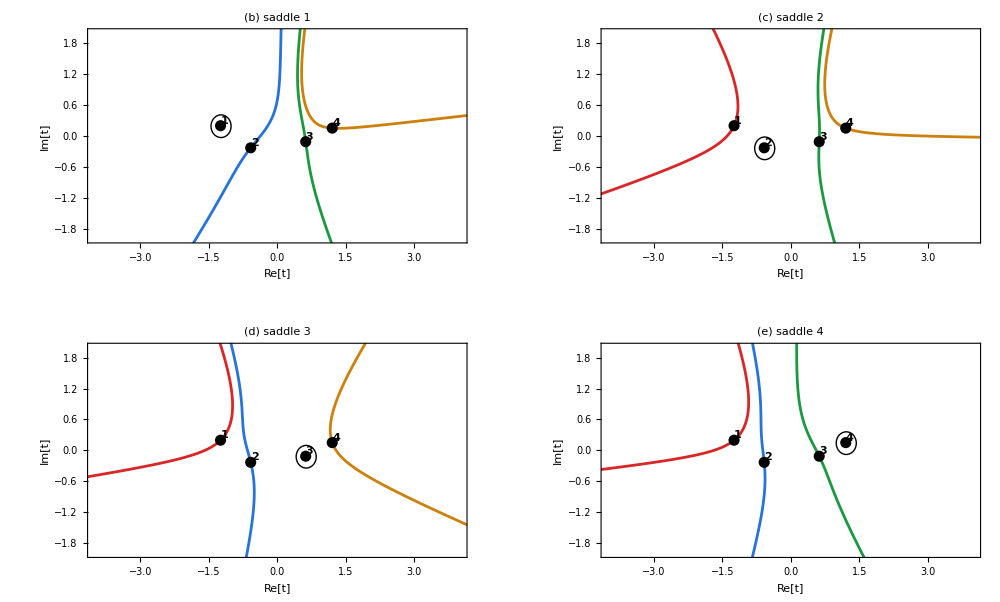

```mathematica
sigmaArg[i_?NumericQ,j_?NumericQ]:=Arg[chiOf[Round[j]]-chiOf[Round[i]]];

descentDirectionsRot[j_,theta_]:=Module[{phi=Arg[fTpp[saddles[[j]]]]},{Exp[I (Pi-phi+theta)/2],Exp[I ((Pi-phi+theta)/2+Pi)]}];

descentRayRot[j_,dir_,theta_,sMax_:8]:=Module[{ti=saddles[[j]],eps=10^-2},NDSolve[{t'[s]==-Conjugate[fTp[t[s]] Exp[-I theta]]/(Abs[fTp[t[s]]]+10^-6),t[0]==ti+eps dir,WhenEvent[Abs[fTp[t[s]]]<10^-3,"StopIntegration"]},t,{s,0,sMax},MaxSteps->10^5][[1]]];

raysForCj[j_,theta_]:=descentRayRot[j,#,theta]&/@descentDirectionsRot[j,theta];

saddleColor={RGBColor[0.85,0.15,0.15],RGBColor[0.15,0.45,0.85],RGBColor[0.10,0.60,0.25],RGBColor[0.80,0.50,0.05]};

(*Figure 2(b)-(e)*)
panelClean[i0_]:=
Module[{i=Round[i0],js,curveGraphics},
js=DeleteCases[Range[4],i];
curveGraphics=Table[{saddleColor[[j]],Thickness[0.005],rayLine/@raysForCj[j,sigmaArg[i,j]]},{j,js}];
Graphics[
{curveGraphics,Black,Thick,Circle[ReIm[saddles[[i]]],0.22],Black,PointSize[0.02],Point[ReIm/@saddles],Black,MapThread[Text[Style[#2,Bold],ReIm[#1],{-1.6,-1.6}]&,{saddles,Range[4]}]},PlotRange->{{-4,4},{-2,2}},Frame->True,FrameLabel->{"Re[t]","Im[t]"},PlotLabel->Row[{"(",FromCharacterCode[97+i],") saddle ",i}
]
]
];

GraphicsGrid[{{panelClean[1],panelClean[2]},{panelClean[3],panelClean[4]}},ImageSize->1000,Spacings->20]
```